```mathematica
Solve[(2-Sqrt[3])p^2+Sqrt[3]p-Sqrt[3]/4==0,p]
```

{{p→(-√2 3^(1/4)+√3)/(2 (-2+√3))},{p→(√2 3^(1/4)+√3)/(2 (-2+√3))}}

```mathematica
%//N
```

{{p→0.241014},{p→-6.70512}}

```mathematica
{p->(-√2 3^(1/4)+√3)/(2 (-2+√3))}//FullSimplify
```

{p→-3/2-√3+√(6+(7 √3)/2)}

```mathematica
1/2-p/.%247//FullSimplify
```

2+√3-√(6+(7 √3)/2)

```mathematica
%//N
```

0.258986

```mathematica
h=1/p/.%247//FullSimplify
```

2+(2 √2)/3^(1/4)

```mathematica
w=1/(1/2-p/.%247)//FullSimplify
```

2+√2 3^(1/4)

```mathematica
2h+2w//Simplify
```

8+(4 √2)/3^(1/4)+2 √2 3^(1/4)

```mathematica
h w//Simplify
```

8+(4 √2)/3^(1/4)+2 √2 3^(1/4)

```mathematica
2h/Sqrt[3]+w//FullSimplify
```

2+(7 √2)/3^(3/4)+4/(√3)

```mathematica
%//N
```

8.65222

```mathematica
4Sqrt[3]//N
```

6.9282

```mathematica
w//N
```

3.86121

```mathematica
h//N
```

4.14914

```mathematica
2+Sqrt[Pi]//N
```

3.77245

```mathematica
sol=Solve[4ss+2Pi rr==ss^2+4ss rr+Pi rr^2]
```

{{ss→1/2 (4-4 rr-√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))},{ss→1/2 (4-4 rr+√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))}}

```mathematica
sol[1]
```

{{ss→1/2 (4-4 rr-√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))},{ss→1/2 (4-4 rr+√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))}}[1]

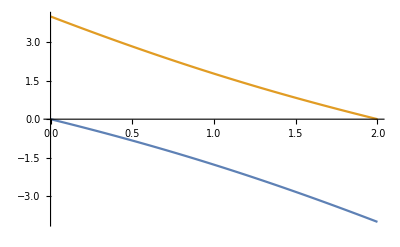

```mathematica
Plot[{ss/.sol[[1]],ss/.sol[[2]]},{rr,0,2}]
```

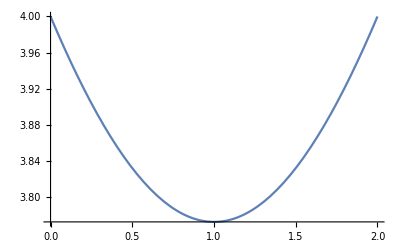

```mathematica
Plot[1/2 (4-4 rr+√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))+2rr,{rr,0,2}]
```

```mathematica
1/2 (4-4 rr+√((-4+4 rr)^2-4 (-2 π rr+π rr^2)))/.rr->1
```

√π

```mathematica
sol=Solve[3ss+2Pi rr==Sqrt[3]/4ss^2+3ss rr+Pi rr^2]
```

{{ss→(12-12 rr-√((-12+12 rr)^2-4 √3 (-8 π rr+4 π rr^2)))/(2 √3)},{ss→(12-12 rr+√((-12+12 rr)^2-4 √3 (-8 π rr+4 π rr^2)))/(2 √3)}}

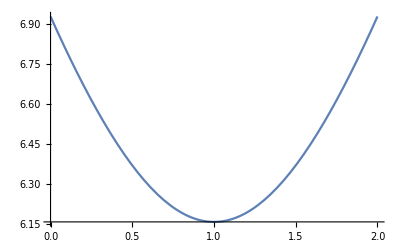

```mathematica
Plot[(12-12 rr+√((-12+12 rr)^2-4 √3 (-8 π rr+4 π rr^2)))/(2 √3)+2Sqrt[3]rr,{rr,0,2}]
```

```mathematica
(12-12 rr+√((-12+12 rr)^2-4 √3 (-8 π rr+4 π rr^2)))/(2 √3)+2Sqrt[3]rr/.rr->1
```

2 √3+(2 √π)/3^(1/4)

```mathematica
%//N
```

6.15765

```mathematica
2Sqrt[3]+2Sqrt[Pi/Sqrt[3]]//N
```

6.15765

```mathematica
(12-12 rr+√((-12+12 rr)^2-4 √3 (-8 π rr+4 π rr^2)))/(2 √3)/.rr->1
```

(2 √π)/3^(1/4)